```mathematica
ClearAll[σRes]
σRes[inA_,inB_,res_,eCM_]:=If[eCM≤m0[inA]+m0[inB],0,
(2j[res]+1)/((2j[inA]+1)(2j[inB]+1)) * Pi/pCMS[eCM,m0[inA],m0[inB]]^2 * Γ[res,{inA,inB},eCM] * breitWigner[Γ[res,eCM],m0[res]-eCM]*If[MemberQ[Ns,res],Sqrt[2/3],Sqrt[1/3]]^2*0.38937966
];
σRes[inA_,inB_,eCM_]:=
Sum[σRes[inA,inB,res,eCM],{res,Join[Ds,Ns]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

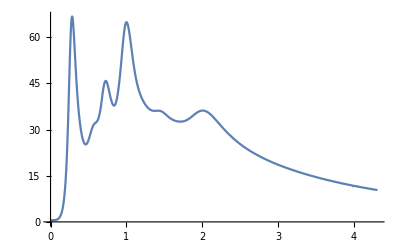

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/NIntegrate/slwcon",
ButtonNote->"NIntegrate::slwcon"]

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsTot=Monitor[
Block[{hA=N938,hB=pi},
Table[{
pLab[m0@hB,m0@hA,eCM],
σRes[hA,hB,eCM]},{eCM,1.,3.,0.003}]
],{res,ProgressIndicator[eCM,{1.,3.}]}
];
ListLinePlot[ptsTot,PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

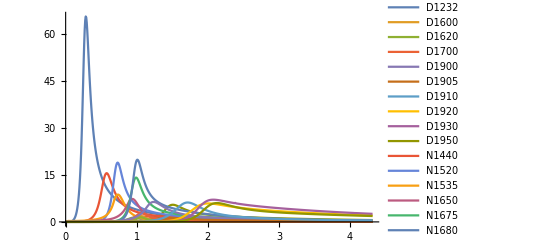

```mathematica
pts=Monitor[
Block[{hA=N938,hB=pi},
Table[{
res,Table[{
pLab[m0[hB],m0[hA],eCM],
σRes[hA,hB,res,eCM]},{eCM,1.,3.,0.005}]
},{res,Join[Ds,Ns]}]
],{res,ProgressIndicator[eCM,{1.,8.}]}
];
ListLinePlot[Second/@pts,PlotLegends->First/@pts,PlotRange->All]
```